```mathematica
(* exploration into Levy SDE *)
```

```mathematica
α=1.5;h=0.1;
```

```mathematica
f[x_] := ArcTan[x]
g[x_] := Sqrt[1+x^2]
```

```mathematica
(* set up initial condition *)
p[x_]:=Evaluate[PDF[NormalDistribution[0,1/10],x]]
ψ[s_]:=Evaluate[InverseFourierTransform[p[x],x,s,FourierParameters->{-1,-1}]]
```

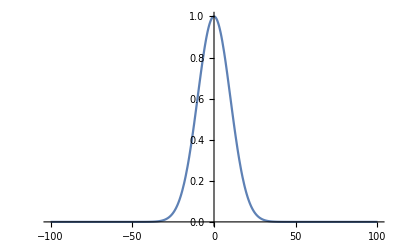

```mathematica
Plot[ψ[s],{s,-100,100},PlotRange->All]
```

```mathematica
bigm=100;
denom=1;
sgrid=Join[Table[i/denom,{i,-bigm,-1}],Table[i,{i,1,bigm}]];
ugrid=Table[i/denom,{i,-bigm,bigm}];
```

```mathematica
ϕ[s_,y_] := Exp[I s (y + f[y] h)] Exp[-h Abs[s g[y]]^α]
```

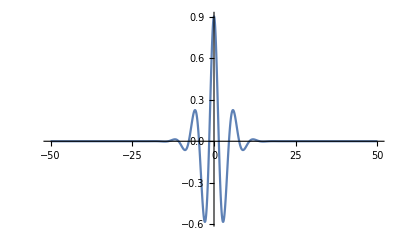

```mathematica
Plot[Re[ϕ[1,y]],{y,-50,50},PlotRange->All]
```

```mathematica
ϕ[1,50]
```

4.34623×10^-16-4.81794×10^-17 ⅈ

```mathematica
<<FourierSeries`
```

```mathematica
bigk[s_,u_]:=NFourierTransform[ϕ[s,y],y,u,FourierParameters->{-1,-1},Method->"TrapezoidalRule"]
```

```mathematica
kmat=Table[bigk[s,u],{s,sgrid},{u,ugrid}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.373114}. NIntegrate obtained -2.74873×10^-7 + 0.\ ⅈ and 4.92028×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.376807}. NIntegrate obtained -1.08989×10^-7 + 0.\ ⅈ and 5.9146×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.380519}. NIntegrate obtained -2.75641×10^-8 + 0.\ ⅈ and 7.02962×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

$Aborted

```mathematica
Dimensions[kmat]
```

{20,21}

```mathematica
vec={Table[0,{i,1,2*bigm+1}]};
vec[[1,bigm+1]]=1;
```

```mathematica
newkmat=Join[kmat[[1;;bigm,1;;(2*bigm+1)]]/(2 π),vec,kmat[[(bigm+1);;(2*bigm),1;;(2*bigm+1)]]/(2π)];
```

```mathematica
newkmat[[10,5]]
```

-0.000647468+1.40611×10^-18 ⅈ

```mathematica
initpsi=Table[{ψ[i]},{i,ugrid}];
N[newkmat.newkmat.newkmat.newkmat.newkmat.initpsi]
```

{{-4.40327×10^-8+1.47197×10^-11 ⅈ},{-1.46659×10^-7+6.0677×10^-11 ⅈ},{-3.73138×10^-7+1.84723×10^-10 ⅈ},{-1.15053×10^-6+7.48109×10^-10 ⅈ},{-3.98236×10^-6+2.47971×10^-9 ⅈ},{-0.0000136314+8.28512×10^-9 ⅈ},{-0.0000403955+2.59767×10^-8 ⅈ},{-0.0000757574+6.88683×10^-8 ⅈ},{0.00045132-1.42944×10^-7 ⅈ},{0.0320729-0.0000880191 ⅈ},{1.+0. ⅈ},{0.0320729+0.0000880191 ⅈ},{0.00045132+1.42944×10^-7 ⅈ},{-0.0000757574-6.88683×10^-8 ⅈ},{-0.0000403955-2.59767×10^-8 ⅈ},{-0.0000136314-8.28512×10^-9 ⅈ},{-3.98236×10^-6-2.47971×10^-9 ⅈ},{-1.15053×10^-6-7.48109×10^-10 ⅈ},{-3.73138×10^-7-1.84723×10^-10 ⅈ},{-1.46659×10^-7-6.0677×10^-11 ⅈ},{-4.40327×10^-8-1.47197×10^-11 ⅈ}}

```mathematica
FourierTransform[Exp[I y(1-y^2)],y,t]
```

(√(π/6) (Abs[1+t]^3 (-BesselI[-1/3,(2 (1+t)^(3/2))/(3 √3)]+BesselJ[-1/3,(2 (1+t)^(3/2))/(3 √3)])+(1+t) √((1+t)^3) (√(1+t) BesselI[-1/3,(2 (1+t)^(3/2))/(3 √3)]+√(1+t) BesselJ[-1/3,(2 (1+t)^(3/2))/(3 √3)]+2 ((1+t)^(3/2))^(1/3) BesselJ[1/3,(2 (1+t)^(3/2))/(3 √3)])))/(3 ((1+t)^(3/2))^(2/3) √((1+t)^3))

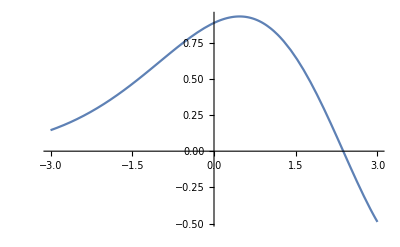

```mathematica
Plot[%,{t,-3,3},PlotRange->All]
```

```mathematica
Plot[- √(2/π) BesselK[1,t Sign[t]] (Sign[t]+t Sign'[t]),{t,-5,5},PlotRange->All]
```

-Graphics-